Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1 - 8 Mean, variance
Find the mean and variance of the random variable X with probability function or density f[x].

1.  f[x] = k x, (0 ≤ x ≤ 2, k suitable)

k is going to need to be 1/2. Since this appears to be a continuous distribution, I have, from numbered line (1) on p. 1035, the formula for mean

```mathematica
mu=Integrate[x^2/2,{x,0,2}]
```

4/3

And the formula for variance

```mathematica
sigsquared=Integrate[(x-mu)^2 x/2,{x,0,2}]
```

2/9

3. Uniform distribution on {0, 2 π}

For a uniform distribution, as in example 1 on p. 1035, the probability of both outcomes are equal, thus 1/2.

```mathematica
Clear["Global`*"]
```

```mathematica
mu=0/2+2π(1/2)
```

π

Example 2 on p. 1036 gives the variance of the uniform distribution as (b - a)^2/12.

```mathematica
sigsquared=(2π-0)^2/12
```

π^2/3

5.  f[x]=4 ⅇ^(-4x) (x≥0)

```mathematica
Clear["Global`*"]
```

```mathematica
pr[x_]=4 ⅇ^(-4x)
```

4 ⅇ^(-4 x)

Checking the pdf to see how it integrates over its domain,

```mathematica
Integrate[pr[x],{x,0,∞}]
```

1

So it looks like it has expected behavior. Trying to calculate the mean from the formula,

```mathematica
mu=Integrate[x pr[x],{x,0,∞}]
```

1/4

Trying to calculate the variance,

```mathematica
sigsquared=Integrate[(x-mu)^2 pr[x],{x,0,∞}]
```

1/16

7.  f[x]=C ⅇ^(-x/2) , (x=0)

```mathematica
Clear["Global`*"]
```

Trying it again.

```mathematica
pr[x_]=C ⅇ^(-x/2)
```

C ⅇ^(-x/2)

Checking the pdf to see how it integrates as a general symbolic integral,

```mathematica
Integrate[pr[x],x]
```

-2 C ⅇ^(-x/2)

I want the integral to equal 1.

```mathematica
Solve[-2 C ⅇ^(-x/2)==1,C]
```

{{C→-ⅇ^(x/2)/2}}

I want to find the value of C.

```mathematica
%/.x->0
```

{{C→-1/2}}

To get the expected pdf, C must equal -1/2. So to check the mean at zero

```mathematica
mu=Integrate[x -ⅇ^(-x/2)/2,x]
```

-1/2 ⅇ^(-x/2) (-4-2 x)

```mathematica
mu1=mu/.x->0
```

2

and the variance

```mathematica
sigsquaredp=Integrate[(x-mu1)^2-ⅇ^(-x/2)/2,x]
```

ⅇ^(-x/2) (4+x^2)

```mathematica
sigsquared=sigsquaredp/.x->0
```

4

Green cells above match the text answer. The constant C, yellow above, has an opposite sign compared with the text answer.

9.  If the diameter X (cm) of certain bolts has the density f[x] = k(x-0.9)(1.1 - x) for 0.9 < x < 1.1 and 0 for other x, what are k, μ, and σ^2 ? Sketch f[x].

```mathematica
Clear["Global`*"]
```

I define the function.

```mathematica
pr[x_]=Piecewise[{{k(x-0.9)(1.1-x), 0.9<x<1.1},{0,1.1≤x},{0,x≤0.9}}]
```

Piecewise[{{k (1.1-x) (-0.9+x), 0.9<x<1.1}, {0, True}}]

I integrate the function over its described interval domain.

```mathematica
Integrate[pr[x],x]
```

Piecewise[{{0., x≤0.9}, {0.324 k-1. k (0.99 x-1. x^2+0.333333 x^3), 0.9<x≤1.1}, {0.00133333 k, True}}]

I solve the integral to find out what k is.

```mathematica
Solve[0.324 k-1. k (0.99 x-1. x^2+0.3333333333333333 x^3)==1,k]/.x->1.1
```

{{k→750.}}

The solution for the integral expression for k gives me, at the upper value of x, the k value shown in the text answer. I plot the function to look at it. Roughly, it looks like the mean should be close to 1. I use NIntegrate to try to find it.

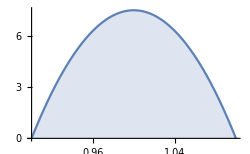

```mathematica
Plot[750 (1.1-x) (-0.9+x),{x,0.9,1.1},Filling->Axis,ImageSize->250]
```

```mathematica
mu=NIntegrate[x(750 (1.1-x) (-0.9+x)),{x,0.9,1.1}]
```

1.

I go on to calculate the variance.

```mathematica
sigsquaredpr=NIntegrate[(x-mu)^2(750 (1.1-x) (-0.9+x)),{x,0.9,1.1}]
```

0.002

The above green cells match the text answer. It seems that NIntegrate is very useful in these circumstances, because regular Integrate was only producting weird-looking stuff.

11. For what choice of the maximum possible deviation from 1.00 cm shall we obtain 10% defectives in problems 9 and 10?

In problem 10, a defective bolt is defined as one that deviates in diameter more than 0.06 cm, that is, with a diameter 0.94 to 1.06.

```mathematica
pr[1]/.k->750
```

7.5

The intention of the following is to find out the number of defectives generated with the k value used in problem 9.

```mathematica
NIntegrate[(750 (1.1-x) (-0.9+x)),{x,0.94,1.06}]
```

0.792

From the following, it looks to me like a little over 20 percent are defective.

```mathematica
1-%
```

0.208

Therefore, it appears that if I want fewer defectives, I have to relax my standards, because I already have over 20% and I want to have only 10%. So I look at it like

```mathematica
Grid[Table[{c,NIntegrate[(750 (1.1-x) (-0.9+x)),{x,0.94-c,1.06+c}]},{c,0.012,0.014,0.0001}],Frame->All]
```

0.012 | 0.893376
0.0121 | 0.894097
0.0122 | 0.894816
0.0123 | 0.895533
0.0124 | 0.896248
0.0125 | 0.896961
0.0126 | 0.897671
0.0127 | 0.89838
0.0128 | 0.899086
0.0129 | 0.89979
0.013 | 0.900492
0.0131 | 0.901191
0.0132 | 0.901888
0.0133 | 0.902584
0.0134 | 0.903277
0.0135 | 0.903967
0.0136 | 0.904656
0.0137 | 0.905342
0.0138 | 0.906026
0.0139 | 0.906708
0.014 | 0.907388

And the amount I would need to relax the standards by seems to be 0.013. So in other words at the low end I would accept

```mathematica
0.94-0.013
```

0.927

I note that I could have set the table up to index directly from 1.0, in which case it would have appeared as

```mathematica
1.0-0.073
```

0.927

and also

```mathematica
1.06+0.013
```

1.073

or

```mathematica
1+0.073
```

1.073

as acceptable, and beyond that the bolts would be defective, and these would represent 10% of the output. The developed results shown in green agree with the text answer.

13.  What is the expected daily profit if a store sells X air conditioners per day with probability f[10] = 0.1, f[11] = 0.3, f[12] = 0.4, f[13] = 0.2 and the profit per conditioner is $55 ?

As noted on http://www-math.bgsu.edu/~albert/m115/probability/average_value.html, when I already have the probabilities assigned to data points, I simply multiply all pairs and sum

```mathematica
data={{10,0.1},{11,0.3},{12,0.4},{13,0.2}}
```

{{10,0.1},{11,0.3},{12,0.4},{13,0.2}}

```mathematica
1+3.3+4.8+2.6
```

11.7

And in this case the sum is leveraged by the profit per item, as

```mathematica
% 55
```

643.5

The green cell above matches the text answer. Though not a factor in the solution in this case, I plot the data points and the probability area.

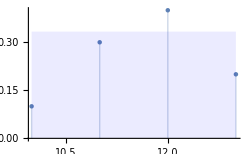

```mathematica
ListPlot[data,Filling->Axis,ImageSize->250,Epilog->{Blue,Opacity[0.08],Polygon[{{10,0},{13,0},{13,1/3},{10,1/3},{10,0}}]}]
```

15.  A small filling station is supplied with gasoline every Saturday afternoon. Assume that its volume X of sales in ten thousands of gallons has the probability density f[x] = 6 x(1 - x) if 0 ≤ x ≤ 1 and 0 otherwise. Determine the mean, the variance, and the standardized variable.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]=Piecewise[{{6x(1-x),0≤x≤1},{0,-∞<x<0},{0,1<x<∞}}]
```

Piecewise[{{6 (1-x) x, 0≤x≤1}, {0, True}}]

I integrate the function over its described interval domain, and find that it checks out.

```mathematica
Integrate[f[x],{x,0,1}]
```

1

I plot the function for general info.

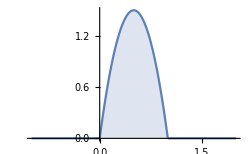

```mathematica
Plot[f[x],{x,-1,2},ImageSize->250,Filling->Axis]
```

I find the mean.

```mathematica
mu=NIntegrate[x f[x],{x,0,1}]
```

0.5

I find the variance.

```mathematica
sigsquaredpr=NIntegrate[(x-mu)^2 f[x],{x,0,1}]
```

0.05

According to numbered line (6) on p. 1037, the standardized random variable Z is given by

Z=(X-μ)/σ

I already have everything, so just plugging in

```mathematica
bigZ=(X-0.5)/(√0.05)
```

4.47214 (-0.5+X)

The green cells above match the answer in the text.

17.  James rolls 2 fair dice, and Harry pays k cents to James, where k is the product of the two faces that show on the dice. How much should James pay to Harry for each game to make the game fair?

```mathematica
Clear["Global`*"]
```

This is a continuous distribution. Probably more than one way to try this, I decide to try making separate events out of the face products. Lot of rambling actions, unsatisfactory until the end, when I try an unusual experiment. See the pink cell below.

```mathematica
un={1,2,3,4,5,6,2,4,6,8,10,12,3,6,9,12,15,18,4,8,12,16,20,24,5,10,15,20,25,30,6,12,18,24,30,36}
Length[un]
```

{1,2,3,4,5,6,2,4,6,8,10,12,3,6,9,12,15,18,4,8,12,16,20,24,5,10,15,20,25,30,6,12,18,24,30,36}

36

```mathematica
uns=Sort[un]
```

{1,2,2,3,3,4,4,4,5,5,6,6,6,6,8,8,9,10,10,12,12,12,12,15,15,16,18,18,20,20,24,24,25,30,30,36}

```mathematica
Total[uns]
```

441

```mathematica
firs=Range[36]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36}

```mathematica
tago=Thread[{firs,uns}]
```

{{1,1},{2,2},{3,2},{4,3},{5,3},{6,4},{7,4},{8,4},{9,5},{10,5},{11,6},{12,6},{13,6},{14,6},{15,8},{16,8},{17,9},{18,10},{19,10},{20,12},{21,12},{22,12},{23,12},{24,15},{25,15},{26,16},{27,18},{28,18},{29,20},{30,20},{31,24},{32,24},{33,25},{34,30},{35,30},{36,36}}

Mathematica gives me a distribution manufactured from the individual data points.

```mathematica
FindDistribution[uns]
```

FindDistribution::conenf: -- Message text not found --

GammaDistribution[1.43293,8.64931]

I can get a PDF function from this.

```mathematica
PDF[GammaDistribution[1.4329281962604636,8.649306552947987],x]
```

Piecewise[{{0.0512813 ⅇ^(-0.115616 x) x^0.432928, x>0}, {0, True}}]

```mathematica
f[x_]=0.051281326827070754 ⅇ^(-0.11561620505393752 x) x^0.43292819626046364
```

0.0512813 ⅇ^(-0.115616 x) x^0.432928

The plot of the function looks reasonable.

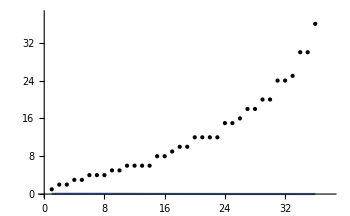

```mathematica
Plot[f[x],{x,1,36},Filling->Axis,ImageSize->350,Epilog->Map[Point,tago],PlotRange->{{0,38},{0,38}},ImagePadding->25]
```

The probability function integration checks out for the full x-axis.

```mathematica
NIntegrate[  f[x],{x,0,∞}]
```

1.

The truncated domain is smaller when integrated.

```mathematica
NIntegrate[  f[x],{x,1,36}]
```

0.93092

The missing area can be compensated for by a k factor.

```mathematica
k=1/%
```

1.07421

When the k factor is included, the area equals 1.

```mathematica
NIntegrate[  k f[x],{x,1,36}]
```

1.

The mean is calculated according to the text formula. This result is considerably different in value than pink cell, below.

```mathematica
mu=NIntegrate[x f[x]k,{x,1,36}]
```

11.5579

Mathematica has a way to get this value directly.

```mathematica
Mean[TruncatedDistribution[{1,36},GammaDistribution[1.4329281962604636,8.649306552947987]]]
```

11.5579

The variance is calculated.

```mathematica
sigsquared=NIntegrate[ k(x-mu)^2 f[x],{x,1,36}]
```

64.6819

The expected value is calculated.

The PDF is plotted. The mean is shown as a red line.

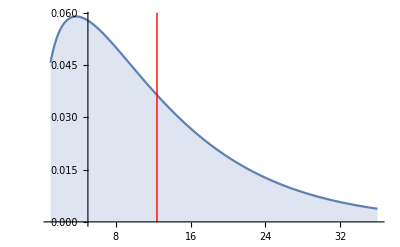

```mathematica
Plot[Evaluate@Table[PDF[GammaDistribution[1.4329281962604636,8.649306552947987],x]],{x,1,36},Filling->Axis,Epilog->{{Red,Line[{{12.3938,0},{12.3938,0.06}}]}}]
```

Out of curiosity, I try out the empirical distribution, which corresponds to the points making up the probability data.

```mathematica
dob=EmpiricalDistribution[uns]
```

DataDistribution[…]

```mathematica
Mean[dob]
```

49/4

```mathematica
N[%]
```

12.25

The mean, thus the expectation, is perfectly aligned with the text answer. The cents to be paid should agree with the expectation, or 12 cents, to the closest cent.

19.  Let X be discrete with probability function f[0] = f[3] = 1/8, f[1] = f[2] = 3/8. Find the expectation of X^3.

```mathematica
Clear["Global`*"]
```

```mathematica
juns={{0,0.125},{1,0.375},{2,0.375},{3,0.125}}
```

{{0,0.125},{1,0.375},{2,0.375},{3,0.125}}

```mathematica
N[54/8]
```

6.75

Numbered line (8) on p. 1038 has the formula for the third moment of X, a special expectation. For the discrete case, it has a formula like

E(X^3)=Sum[x_j^3 f[x_j]], which in the present case would consist of

```mathematica
(0^3*0.125+1^3*0.375+2^3*0.375+3^3*0.125)
```

6.75

The above green cell matches the answer in the text. Mathematica has a command for Moment, and it does pertain to statistics, but I could not get it to produce the desired answer.